```mathematica
(**********************************************************************************)
```

```mathematica
(* Example 1 *)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(* Drawing y = x - 1/x *)
```

```mathematica
xx=Table[0.1+(4-0.1)/(40-1)(i-1),{i,1,40}]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.}

```mathematica
Length[xx]
```

40

```mathematica
yy=Table[xx[[i]]-1/xx[[i]],{i,1,40}]
```

{-9.9,-4.8,-3.03333,-2.1,-1.5,-1.06667,-0.728571,-0.45,-0.211111,-3.33067×10^-16,0.190909,0.366667,0.530769,0.685714,0.833333,0.975,1.11176,1.24444,1.37368,1.5,1.62381,1.74545,1.86522,1.98333,2.1,2.21538,2.32963,2.44286,2.55517,2.66667,2.77742,2.8875,2.99697,3.10588,3.21429,3.32222,3.42973,3.53684,3.64359,3.75}

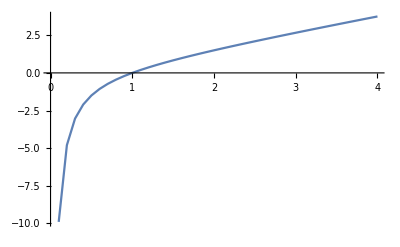

```mathematica
ListPlot[Table[{xx[[i]],yy[[i]]},{i,1,40}],Joined->True]
```

```mathematica
y[x_]:=x-1/x
```

```mathematica
inty=Integrate[y[x],{x,1,4}]
```

15/2-Log[4]

```mathematica
N[inty]
```

6.11371

```mathematica
(* Generating random samples *)
```

```mathematica
Clear[y]
```

```mathematica
m=100;
```

```mathematica
Random[]
```

0.0914364

```mathematica
x=Table[1+(4-1)Random[],{i,1,m}];
```

```mathematica
y=Table[3.75Random[],{i,1,m}];
```

```mathematica
(* Drawing the generated random samples *)
```

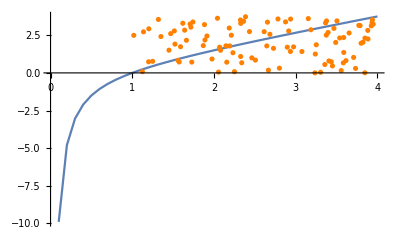

```mathematica
Show[ListPlot[Table[{xx[[i]],yy[[i]]},{i,1,40}],Joined->True],ListPlot[Table[{x[[i]],y[[i]]},{i,1,m}],PlotStyle->Orange]]
```

```mathematica
(* Total and sample area *)
```

```mathematica
totalarea=(4-1)*3.75
```

11.25

```mathematica
samplearea=totalarea/m
```

0.1125

```mathematica
(* Target area *)
```

```mathematica
s=0;
```

```mathematica
For[i=1,i≤m,i++,
If[y[[i]]≤x[[i]]-1/x[[i]],s=s+1];
]
Print[s]
```

56

```mathematica
targetarea=s*samplearea
```

6.3

```mathematica
(**********************************************************************************)
```

```mathematica
(* Example 2 *)
```

```mathematica
Clear["Global`*"]
```

```mathematica
cauchy[theta_]:=1/(1+theta^2)
```

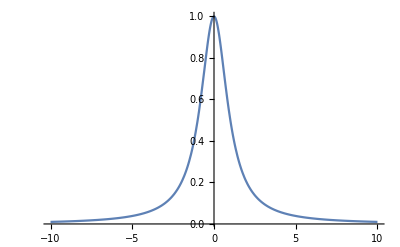

```mathematica
Plot[cauchy[theta],{theta,-10,10},PlotRange->All]
```

```mathematica
(* Initiation of Metropolis algorithm *)
```

```mathematica
T=500; (* Maximum number of iterations *)
```

```mathematica
sigma=1; (* Standard deviation of Normal proposal density *)
```

```mathematica
thetamin=-30; thetamax=30; (* Define a range for theta *)
```

```mathematica
theta=Table[0,{i,1,500}]; (* Storage space for the samples *)
```

```mathematica
theta[[1]]=RandomReal[{-30,30}]; (* Generate the initial value *)
```

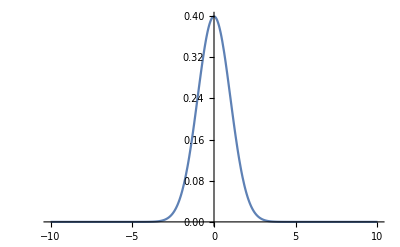

```mathematica
Plot[PDF[NormalDistribution[0,sigma],x] ,{x,-10,10},PlotRange->All]
```

```mathematica
(* Generation of random numbers with Gaussian (random) distribution *)
```

```mathematica
PGaussian[x_,μ_,σ_]:=1/(√(2π)σ)Exp[-(x-μ)^2/(2 σ^2)]
```

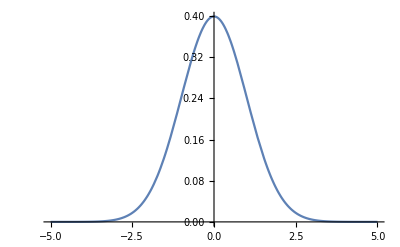

```mathematica
Plot[PGaussian[x,0,1],{x,-5,5},PlotRange->All]
```

```mathematica
NIntegrate[PGaussian[x,0,1],{x,-5,5}]
```

0.999999

```mathematica
NormalRandom[μ_,σ_]:=Module[{x,y},
While[True,
x=μ-5σ+(10σ)RandomReal[];
y=RandomReal[];
If[y≤ PGaussian[x,μ,σ],Break[]];
];
Return[x];
]
```

```mathematica
NormalRandom[0,1]
```

-3.01358

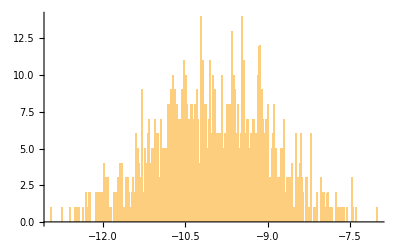

```mathematica
Histogram[Table[NormalRandom[-10,1],{i,1,1000}],200]
```

```mathematica
(* Start sampling *)
```

```mathematica
t=1;
While[t<T,
t=t+1;
thetastar=NormalRandom[theta[[t-1]],sigma] (* Generating proposal *); 
alpha = Min[1,cauchy[thetastar]/cauchy[theta[[t-1]]]];
u = Random[];
If[u<alpha,theta[[t]]=thetastar,theta[[t]]=theta[[t-1]]];
]
```

```mathematica
(* Plot *)
```

```mathematica
(* Display histogram of samples *)
```

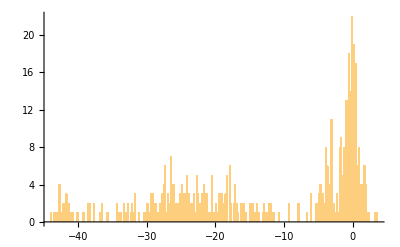

```mathematica
Histogram[theta,200]
```

```mathematica
nbins = 200;
```

```mathematica
thetabins=Table[N[thetamin+(thetamax-thetamin)/(nbins-1)(i-1)],{i,1,nbins}];
```

```mathematica
deltatheta=N[(thetamax-thetamin)/nbins]
```

0.3

```mathematica
counts=BinCounts[theta,{thetamin,thetamax,deltatheta}];
```

```mathematica
Length[counts]
```

200

```mathematica
sumcounts=Sum[counts[[i]],{i,1,nbins}]
```

447

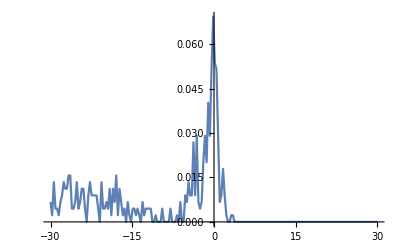

```mathematica
ListPlot[Table[{thetabins[[i]],counts[[i]]/sumcounts},{i,1,nbins}],Joined->True,PlotRange->All]
```

```mathematica
(* Theoretical density *)
```

```mathematica
y=Table[cauchy[thetabins[[i]]],{i,1,nbins}];
```

```mathematica
sumy=Sum[y[[i]],{i,1,nbins}]
```

10.1997

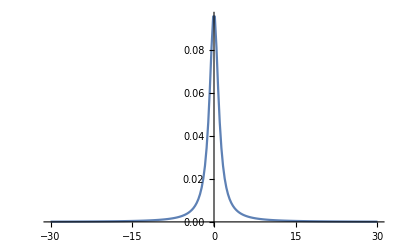

```mathematica
ListPlot[Table[{thetabins[[i]],y[[i]]/sumy},{i,1,nbins}],Joined->True,PlotRange->All]
```

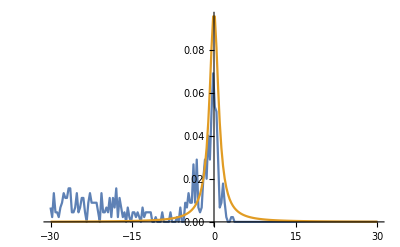

```mathematica
ListPlot[{Table[{thetabins[[i]],counts[[i]]/sumcounts},{i,1,nbins}],Table[{thetabins[[i]],y[[i]]/sumy},{i,1,nbins}]},Joined->True,PlotRange->All]
```

```mathematica
(* Display the history of samples *)
```

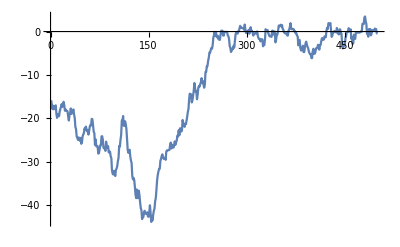

```mathematica
ListPlot[Table[{i,theta[[i]]},{i,1,T}],Joined->True]
```

```mathematica
(**********************************************************************************)
```

```mathematica
(* Example 3 *)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(* bivexp *)
```

```mathematica
lambda1=0.5;
lambda2=0.1;
lambda=0.01;
maxval=8.0;
```

```mathematica
bivexp[theta1_,theta2_]:=Exp[-(lambda1+lambda)theta1+-(lambda2+lambda)theta2-lambda maxval]
```

```mathematica
Plot3D[bivexp[theta1,theta2],{theta1,0,8},{theta2,0,8}]
```

-Graphics3D-

```mathematica
(* BWU *)
```

```mathematica
(* Initiation of blockwise updating *)
```

```mathematica
T=5000; (* Maximum number of iterations *)
```

```mathematica
thetamin={0,0}; (* Min of theta1 and theta2 *)
```

```mathematica
thetamax={8,8}; (* Max of theta1 and theta2 *)
```

```mathematica
theta={Table[0,{t,1,T}],Table[0,{t,1,T}]}; (* Storage space for samples *)
```

```mathematica
RandomReal[{thetamin[[1]],thetamax[[1]]}]
```

1.82642

```mathematica
theta[[1,1]]=RandomReal[{thetamin[[1]],thetamax[[1]]}]; (* Generate initial value for theta1 *)
```

```mathematica
theta[[2,1]]=RandomReal[{thetamin[[2]],thetamax[[2]]}]; (* Generate initial value for theta2 *)
```

```mathematica
(* Start sampling *)
```

```mathematica
t=1;
While[t<T,
t=t+1;
thetastar={RandomReal[{thetamin[[1]],thetamax[[1]]}],RandomReal[{thetamin[[2]],thetamax[[2]]}]}; (* Generate proposal *);
fraction=bivexp[thetastar[[1]],thetastar[[2]]]/bivexp[theta[[1,t-1]],theta[[2,t-1]]];
alpha=Min[1,fraction];
u=RandomReal[];
If[u≤ alpha,
theta[[1,t]]=thetastar[[1]];
theta[[2,t]]=thetastar[[2]];,
theta[[1,t]]=theta[[1,t-1]];
theta[[2,t]]=theta[[2,t-1]];
];
]
```

```mathematica
(* Plot *)
```

```mathematica
(* Display histogram of samples *)
```

```mathematica
nbins=10;
```

```mathematica
thetabins1=Table[N[thetamin[[1]]+(thetamax[[1]]-thetamin[[1]])/(nbins-1)(i-1)],{i,1,nbins}];
```

```mathematica
thetabins2=Table[N[thetamin[[2]]+(thetamax[[2]]-thetamin[[2]])/(nbins-1)(i-1)],{i,1,nbins}];
```

```mathematica
counts={};
For[i=1,i≤nbins-1,i++,
For[j=1,j≤nbins-1,j++,
countsij=0;
For[t=1,t≤T,t++,
If[
(thetabins1[[i]]≤ theta[[1,t]]<thetabins1[[i+1]])&&(thetabins2[[j]]≤ theta[[2,t]]<thetabins2[[j+1]]),
countsij=countsij+1;
];
];
counts=Join[counts,{{thetabins1[[i]],thetabins2[[j]],countsij}}];
];
];
```

```mathematica
ListPointPlot3D[counts]
```

-Graphics3D-

```mathematica
(* Plot the theoretical density *)
```

```mathematica
nbins=20;
```

```mathematica
thetabins1=Table[N[thetamin[[1]]+(thetamax[[1]]-thetamin[[1]])/(nbins-1)(i-1)],{i,1,nbins}];
```

```mathematica
thetabins2=Table[N[thetamin[[2]]+(thetamax[[2]]-thetamin[[2]])/(nbins-1)(i-1)],{i,1,nbins}];
```

```mathematica
theta1theta2y=Table[{thetabins1[[i]],thetabins2[[j]],bivexp[thetabins1[[i]],thetabins2[[j]]]},{i,1,nbins},{j,1,nbins}];
```

```mathematica
ListPointPlot3D[theta1theta2y]
```

-Graphics3D-

```mathematica
Show[ListPointPlot3D[counts],ListPointPlot3D[theta1theta2y]]
```

-Graphics3D-

```mathematica
(**********************************************************************************)
```